```mathematica
magic[primeList_] :=magic[primeList] =N[(∏_p^primeList (1/p+1)^(1/(log(p))))/(2^(∑_p^primeList 1/(log(p))))]
```

```mathematica
myFactor [n_]:=myFactor [n]= Join[Flatten[Table[Table[f[[1]], {i,1, 1}], {f, FactorInteger[n]}]],1]
```

```mathematica
myFactor[12]
```

{2,2,3}

```mathematica
Table[Table[f[[1]], {i,1, f[[2]]}], {f, FactorInteger[12]}]
```

{{2,2},{3}}

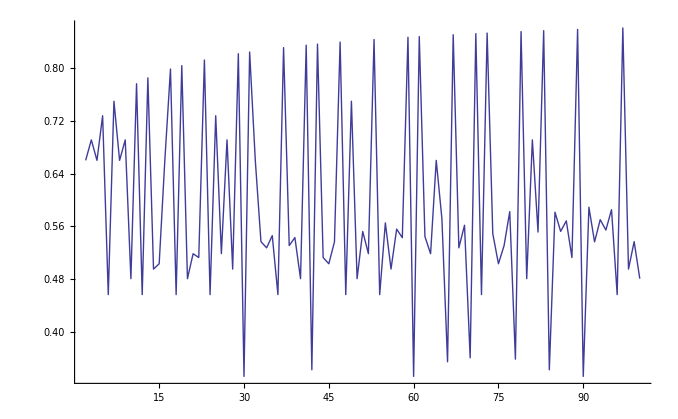

```mathematica
ListPlot[
Table[{i,magic[myFactor[i]]},{i,2,100}],
Joined->True
]
```

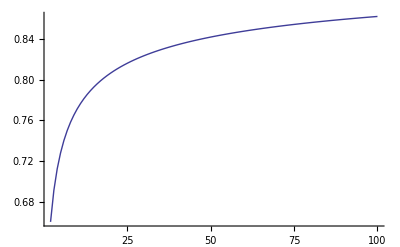

```mathematica
ListPlot[
Table[{i,magic[{i}]},{i,2,100}],
Joined->True
]
```

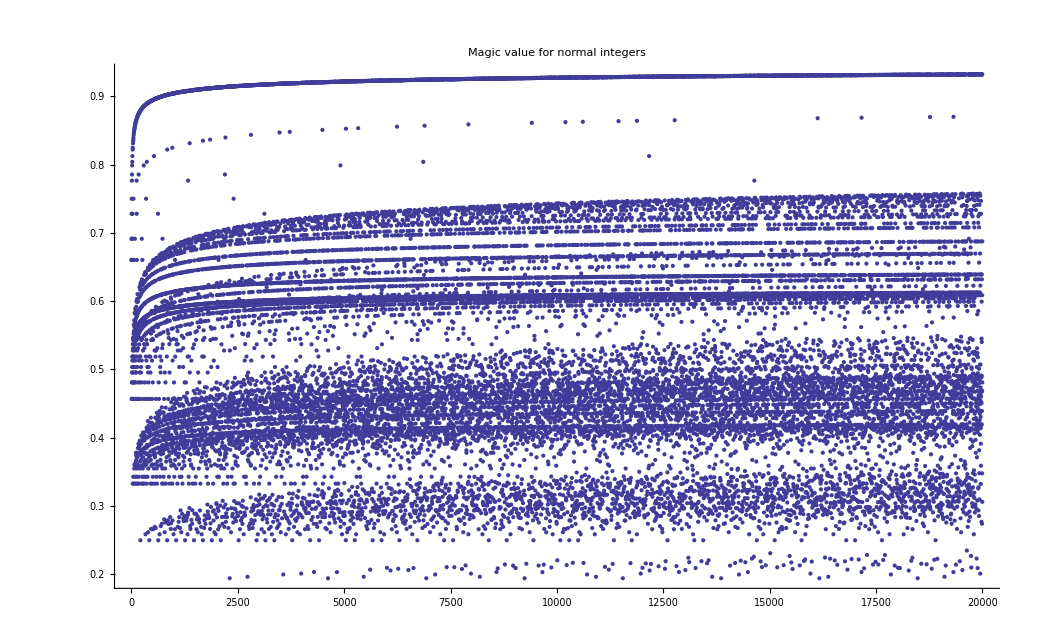

```mathematica
ListPlot[
Table[{i,magic[myFactor[i]]},{i,2,20000}],
GridLines->{Automatic, {{1/E,{Red, Thick}}}},
PlotLabel->"Magic value for normal integers",
			LabelStyle->{FontFamily->"Calibri", FontSize->Larger}
]
```

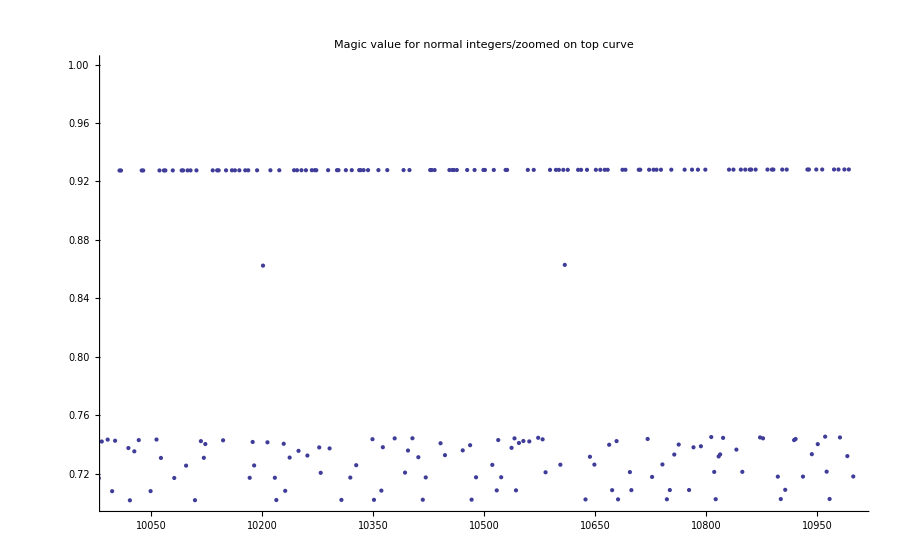

```mathematica
ListPlot[
Table[{i,magic[myFactor[i]]},{i,2,11000}],
GridLines->{Table[Prime[q],{q,1,2000,1}], {{1/E,{Red, Thick}}}},
PlotRange->{{10000,11000},{0.7,1.0}},
PlotLabel->"Magic value for normal integers/zoomed on top curve",
			LabelStyle->{FontFamily->"Calibri", FontSize->Larger}
]
```

```mathematica
magic[{97,101}]
```

0.742798

```mathematica
Select[Sort[Table[{magic[myFactor[i]]-1/E,i,myFactor[i]}, {i,2,200000}]], Abs[#[[1]]]<10^-5&]
```

{{-9.21339×10^-6,142058,{2,7,73,139}},{-5.40039×10^-6,106395,{3,5,41,173}},{2.67336×10^-6,119054,{2,13,19,241}},{7.83374×10^-6,75831,{3,7,23,157}}}

```mathematica
N[magic[{31,37,59,79,89,97}]-1/E]
```

-4.19068×10^-6

```mathematica
MyList[n_,p_]:=ReadList[StringJoin["d:\\Triangle\\Data\\",ToString[n], "\\",ToString[n],"_",ToString[p],".txt"],Number,200]
```

```mathematica
data=MyList[4,7]
```

{0,1,2,3,56,57,58,364,365,408,409,5491,36179,36183,36184,6033811,6033812,6033813,6033833,6033834,6033835,900190515,900190516,900190566,900190567,2594285750,2594285751,2594285752,2594285765,712139413975,712139413979,712139413988,712139413989,712139414470,712139414471,712139414472,712139414483,712139414484,712139414485,712139414486,10955278810686,10955280445011,10955280445032,1933946779751779,1933946779751780,1933946779771413,1933946779771414,1933946779771415,1933946779771426,1933946779771427,1933946779771428,1933946779771765,1967849470514788,1967849470514789,1967849470514790,1967849470514840,229566046708785858468365761,229566046708785858468365762,229566046708785858468365774,229566046708785858468365775,229566046708785858468365776,229566046708785858468366102,229566046708785858468366103,229566046708785858468366112,229566046708785858468366116,229566046708785858468366117,229566046708785858468366389,229566046708785858468366390,229566046708785858468366391,229566046708785858469789952,229566046708785858469789953,229566046708785858469789954,229566046708785870684551548,229566046708785870684565211,229566046708785870684565217,229566046708785870684565230,2354597448209351273602203680072883205733943,2354597448209351273602203680072883205737471,2354597448209351273602203680072883205737472,2354597448209351273602203680072883206087625,2354597448209351273602203680072883206087626,2354597448209351273602203680072883206087627,2354597448209351273602203680072883211771135,2354597448209351273602203680072883211771136,2354597448209351273602203680072883211771149,2354597448242649789533612952116267774979665,2354597448242649789533612952116267774979666,2354597448242649789533612952116269464885150,2354597448242649789533612952116269464885151,2354597448242649789533612952116269464885169,2354597448242649789533612952116269464885204,2354597448242649789533612952116269464885205,306793257509014115798191744010119797896742832473,306793257528936704771350033337949769541468869350,306793257528936704771350033337949769541468869351,306793257528936704771350033337949769541468869352,306793257528936704771350033337949769541468869364,306793257528936704771350033337949769541468869365,306793257528936704771350033337949769541468869366,306793257528936704771350033337949769541468869706,306793257528936704771350033337949769541468869757,306793257528936704771350033337949769541468869758,17971075276842363141400979140100575962049525944932001234796831430764043,17971075276842363141400979140100575962049525944932001789995334166589924,17971075276842363141400979140100575962049525944932001789995334166589967,17971075276842363141400979140100575962049525944932001803018571943059066,17971075276842363141400979140100575962049525944932001803018571943059083,17971075276842363141400979140100575962049525944932001803018571943747222,17971075276842363141400979140100575962049525944932001803018571943747223,17971075276842363141400979140100575962049525944932001803018571943747224,17971075276842363141400979140100575962049525944932001803018571943747225,17971075276842363141400979140100575962049525944932001803018668309245857,17971075276842363141400979140100575962049525944932001803018668309245858,17971075276842363141400979140100575962049525944932001803018668309245892,17971075276842363141400979140100575962049525944932001803018668309245893,17971075276842363141400979140100575962049525944932001803018668309245894,17971075276842363141400979140100575962049525944932001803018668309245895,17971075276842363141400979140100575962049525944932001803018698569246078,17971075276842363141400979140100575962049525944932001803018698569246082,17971075276842363141400979140100575962049525944932001803018698569248135,17971075276842363141400979140100575962049525944932001803018698569248136,17971075276842363141400979140100575962049525944932001803056852800408843,17971075276842363141400979140100575962049525944932001803056852800408844,17971075276842363141400979140100575962049525944932001803056852800409130,17971075276842363141400979140100575962049525944932001803056852800409131,17971075276842363141400979140100575962049525944932001803056852800422507,17971075276842363141400979140100575962049525944932201942953779863139295,17971075276842363141400979140100575962049525944932201942953779863140987,17971075276842363141400979140100575962049525944932201942953779863140988,17971075276842363141400979140100575962049525944932201942953779863140989,17971075276842363141401100162956084577725106923388116064688109770553704,17971075276842363141401100162956084577725106923388116064688109770553738,17971075276842363141401100162956084577725106923388116064688109770553739,17971075276842363141401100162956084577725106923388116064688109770553740,17971075276842363141401100162956084577725106923388116064688109770553741,17971075276842363141401100162956084577725106923388116064688109770554049,987237571886409516564612292787298523778234008606963100480478235918284940,987237571886409516564612292787298523778234008606963100480478235918290035,987237571886409516564612292787298523778234008606963100480478235918290036,987237571886409516564612292787298523778234008606963100480478235918624119}

```mathematica
ListPlot[Table[magic[myFactor[i]], {i, data}], Joined->True]
```

Power::infy: Infinite expression 1/0 encountered.

∞::indet: Indeterminate expression ComplexInfinity^0 encountered.

Power::infy: Infinite expression 1/0 encountered.

∞::indet: Indeterminate expression 2^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power will be suppressed during this calculation.

∞::indet: Indeterminate expression 2^ComplexInfinity encountered.

General::stop: Further output of indet will be suppressed during this calculation.

$Aborted

```mathematica
magic[myFactor[Binomial[20,10]]]
```

0.170902

```mathematica
magic[myFactor[10]]
```

0.480739